```mathematica
file=Import["C:\\Users\\em1120\\DisplacedMolecularDocking\\DisplacedGBS_4uxb\\Adjacency_matrix _tau1.1_test.CSV","Data"]
```

{{1,0,0,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1},{0,1,1,1,1,1,1,1,1},{1,1,1,1,0,0,1,1,1},{1,1,1,0,1,1,1,1,1},{1,1,1,0,1,1,1,1,1},{1,1,1,1,1,1,1,0,0},{1,1,1,1,1,1,0,1,1},{1,1,1,1,1,1,0,1,1}}

{0.11658,0.387,0.42684,0.387,0.32868,0.40116,0.42864,0.40116,0.31464}

```mathematica
MatrixWeights=Flatten[Import["C:\\Users\\em1120\\DisplacedMolecularDocking\\DisplacedGBS_4uxb\\weights.csv","CSV"]]*0.6
integers=Table[i,{i,1,Length[MatrixWeights]}]
rules=Diagonal[Thread[integers-> #]  &/@MatrixWeights]
```

{0.11658,0.387,0.42684,0.387,0.32868,0.40116,0.42864,0.40116,0.31464}

{1,2,3,4,5,6,7,8,9}

{1→0.11658,2→0.387,3→0.42684,4→0.387,5→0.32868,6→0.40116,7→0.42864,8→0.40116,9→0.31464}

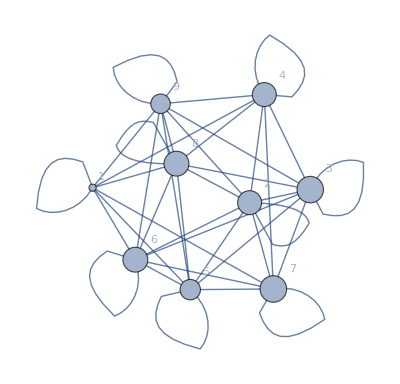

C:\Users\em1120\DisplacedMolecularDocking\DisplacedGBS_4uxb\graph.PNG

Export::noopen: Cannot open C:\Users\em1120\DisplacedMolecularDocking\DisplacedGBS_4uxb\graph.PDF.

$Failed

C:\Users\em1120\DisplacedMolecularDocking\DisplacedGBS_4uxb\graph.SVG

```mathematica
graph=AdjacencyGraph[file,VertexSize->rules,VertexLabels->"Name"]
Export["C:\\Users\\em1120\\DisplacedMolecularDocking\\DisplacedGBS_4uxb\\graph.PNG",graph]
Export["C:\\Users\\em1120\\DisplacedMolecularDocking\\DisplacedGBS_4uxb\\graph.PDF",graph]
```

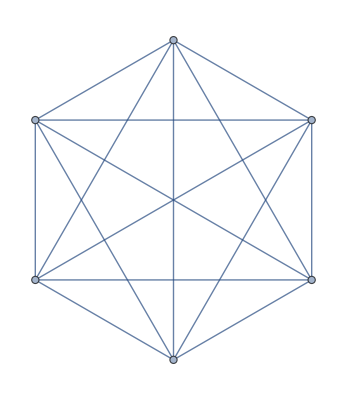

```mathematica
A=CompleteGraph[6]
```

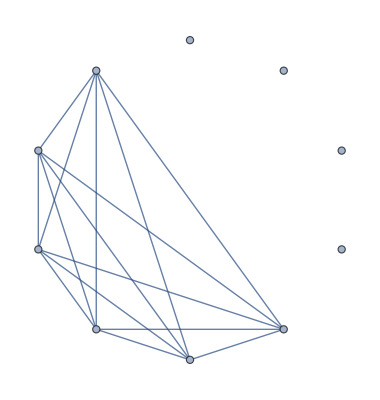

```mathematica
A=VertexAdd[A,{a,b,c,d}]
```

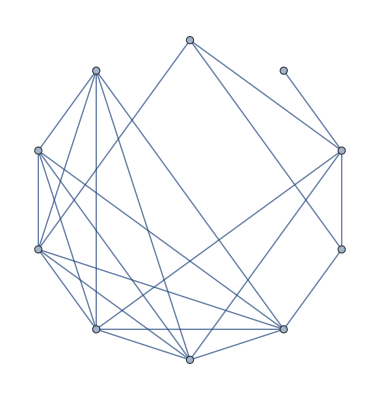

```mathematica
B=EdgeAdd[A,{UndirectedEdge[a,b],UndirectedEdge[b,c],UndirectedEdge[b,d],UndirectedEdge[5,b],UndirectedEdge[4,b],UndirectedEdge[d,3],UndirectedEdge[a,d],UndirectedEdge[a,6]}]
```

```mathematica
Export["C:\\Users\\em1120\\DisplacedMolecularDocking\\DisplacedGBS_4uxb\\max_clique.PNG",B]
```

C:\Users\em1120\DisplacedMolecularDocking\DisplacedGBS_4uxb\max_clique.PNG